# Kerr Total-Transmission Modes Right

Right total-transmission modes of the Kerr geometry can be computed using the KerrTTMR` package, building upon the common framework provided by the KerrTTMR` package.

## The Teukolsky radial equation

Building on the framework outlined in Modes of the Kerr Geometry, KerrTTMR` package make the following specific choices which cause the package to find right total-transmission modes:

ζ=ζ_-=-ⅈ ω, 
ξ=ξ_-=-s-ⅈ σ_+, 
η=η_+=-ⅈ σ_-.

With these choices, the recurrence relation coefficients α_n, β_n, and γ_n are uniquely determined.  The KerrTTMR` package also provides the routine RadialCFRemainder which provides an estimate for r_N appropriate for computing right total-transmission modes.  Together, these provide the definitions necessary to compute the truncated continued fraction Cf(n,N).

For total-transmission modes, a polynomial equation may be used in place of the continued fraction.  Which type of function will be used in solving the radial equation is determined by the SelectMode function which must be called before any other calls to the KerrTTMR` package.  When SelectMode[ContinuedFractionMode] is used, the usual truncated continued fraction Cf(n,N) is used in solving the radial equation.  When SelectMode[PolynomialMode] is used, the modes of the radial equation are determined by the vanishing of the Starobinsky constant (|𝒞|)^2 where

(|𝒞|)^2=Piecewise[{{(ƛ̂)^2(ƛ̂+2)^2+8 ƛ̂ a ω(6(a ω+m)-5 ƛ̂(a ω-m))+144 ω^2(M^2+(a^2(a ω-m))^2), s=±2}, {(ƛ̂)^2-4 a ω (a ω-m), s=±1}}],

where

ƛ̂=Piecewise[{{ƛ=_s A_(ℓ,m)(a ω)+a^2 ω^2-2a m ω, s<=0}, {_s A_(ℓ,m)(a ω)+a^2 ω^2-2a m ω+2s, s>0}}].

The notation for the Starobinsky constant  (|𝒞|)^2 can be confusing.  The notation follows Chandrasekhar (1984) where 𝒞_1 𝒞_2≡(|𝒞|)^2 is, in general, a complex number, but is real for an algebraically special mode.

## Supplying Initial Guesses

Finding any mode requires an initial guess for the mode frequency ω and the separation constant _s A_(ℓ,m)(c).  When a mode sequence does not already exist the ModeaStart option to KerrTTMRSequence can be used to provide an initial guess at any value of the Kerr rotation parameter a.  Subsequent initial guesses for extending a sequence will be computed automatically from existing mode solutions.  On occasion, automatically generated guesses may fail.  In this case, the process of extending the sequence can be restarted and the ModeGuess option can be used to supply an alternative initial guess for the next value of a which will be attempted.

If the ModeaStart option is not used when creating a new sequence, then the new sequence will be started from the Schwarzschild limit a=0, and initial guesses will be taken from the global variable SchXXXTable.  The routine SchwarzschildTTMR is provided to refine guesses already stored in  SchXXXTable.

Create a minimal table of Schwarzschild gravitational TTMRs.

```mathematica
Needs["KerrTTMR`"]
```

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
SetSpinWeight[2]
```

All KerrMode routines (TTMR) set for Spin-Weight s = 2

```mathematica
For[l=2,l<=5,++l,
SchTTMRTable[l,0]={-ⅈ/12(l-1)l(l+1)(l+2),0};
SchTTMRTable[l,1]={-ⅈ/12(l-1)l(l+1)(l+2),1};
SchTTMRTable[l]=2;
]
```

```mathematica
For[l=2,l<=5,++l,
	SchwarzschildTTMR[l,0];
]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

Computing (l=3,n=0)

{-10. ⅈ,0,300,-14,0}

Computing (l=4,n=0)

{-30. ⅈ,0,300,-14,0}

Computing (l=5,n=0)

{-70. ⅈ,0,300,-14,0}

Now create the ℓ=2, m=2, n=0 TTMR sequence with an accuracy of 10^-5.

```mathematica
KerrTTMRSequence[2,2,0,-5]
```

Set $MinPrecision = 24

Starting KerrTTMR[2,2,0] sequence

ModeSol a=0. ω=0.-2. ⅈ Alm=0.

No solution found at a = 0.001, try decreasing Δa, blevel = 1

NKMode <= 2 : index0 = 0

ModeSol+/- a=0.0005 ω=0.00266666-1.99999 ⅈ Alm=-2.8201×10^-6+0.00266666 ⅈ

ModeSol a=0.001 ω=0.00533324-1.99998 ⅈ Alm=-0.0000112803+0.00533329 ⅈ

Increasing Δa, blevel = 0

ModeSol a=0.002 ω=0.0106659-1.99992 ⅈ Alm=-0.000045119+0.0106664 ⅈ

ModeSol a=0.003 ω=0.0159975-1.99982 ⅈ Alm=-0.00010151+0.0159989 ⅈ

```mathematica
⋮
```

Decreasing Δa, blevel = 8

ModeSol a=0.99999609375 ω=0.631846-0.571641 ⅈ Alm=-1.71891+2.08487 ⅈ

ModeSol+ a=0.999994140625 ω=0.631846-0.571642 ⅈ Alm=-1.7189+2.08487 ⅈ

ModeSol- a=0.999990234375 ω=0.631847-0.571644 ⅈ Alm=-1.7189+2.08486 ⅈ

Decreasing Δa, blevel = 9

ModeSol a=0.999998046875 ω=0.631845-0.57164 ⅈ Alm=-1.71891+2.08487 ⅈ

ModeSol+ a=0.9999970703125 ω=0.631846-0.57164 ⅈ Alm=-1.71891+2.08487 ⅈ

ModeSol- a=0.9999951171875 ω=0.631846-0.571641 ⅈ Alm=-1.7189+2.08487 ⅈ

Decreasing Δa, blevel = 10

ModeSol a=0.9999990234375 ω=0.631845-0.57164 ⅈ Alm=-1.71891+2.08487 ⅈ

Initial guesses can also be obtained from contour plots of the mode function.

Plot the real and imaginary zero contours of the mode function at a=1/10 with s=2, m=3, and using the 3rd eigenvalue in the list of separation constants. Total-transmission modes can use the continued fraction method when modes are not on the imaginary axis.

```mathematica
$MinPrecision=24;
```

```mathematica
SelectMode[ContinuedFractionMode]
```

Mode set to find Continued Fraction solutions

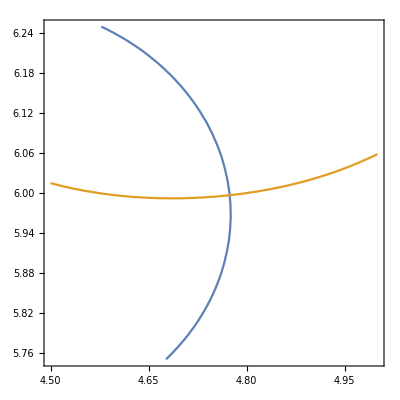

```mathematica
ContourPlot[{Re[PlotModeFunctionIndex[0,2,3,9/10,3,ωr-ⅈ ωi,300,30]]==0,Im[PlotModeFunctionIndex[0,2,3,9/10,3,ωr-ⅈ ωi,300,30]]==0},{ωr,4.5`24,5.0`24},{ωi,5.75`24,6.25`24}]
```

```mathematica
AngularSpectralRootIndex[2,3,9/10(4.77-6.00ⅈ),3,30][[1]]
```

28.2758+25.4335 ⅈ

Use ω=4.77-6.00ⅈ and _2 A_(4,3)=28.3+25.4 ⅈ as an initial guess at a=9/10 and solve for the sequence in the forward direction.

```mathematica
SelectMode[ContinuedFractionMode]
```

Mode set to find Continued Fraction solutions

```mathematica
KerrTTMRSequence[4,3,1,-5,ModeaStart->{9/10,4.77-6.00ⅈ,28.3+25.4ⅈ},SeqDirection->Forward]
```

Starting KerrTTMR[4,3,1] sequence

ModeSol a=0.9 ω=4.7739-5.99668 ⅈ Alm=28.2264+25.4622 ⅈ

ModeSol a=0.901 ω=4.76921-5.98986 ⅈ Alm=28.2224+25.468 ⅈ

ModeSol a=0.902 ω=4.76453-5.98305 ⅈ Alm=28.2184+25.4738 ⅈ

ModeSol a=0.903 ω=4.75986-5.97627 ⅈ Alm=28.2144+25.4796 ⅈ

```mathematica
⋮
```

Decreasing Δa, blevel = 8

ModeSol a=0.99999609375 ω=4.34922-5.38309 ⅈ Alm=27.8424+26.0123 ⅈ

ModeSol+ a=0.999994140625 ω=4.34923-5.3831 ⅈ Alm=27.8424+26.0123 ⅈ

ModeSol- a=0.999990234375 ω=4.34924-5.38312 ⅈ Alm=27.8424+26.0123 ⅈ

Decreasing Δa, blevel = 9

ModeSol a=0.999998046875 ω=4.34921-5.38308 ⅈ Alm=27.8424+26.0124 ⅈ

ModeSol+ a=0.9999970703125 ω=4.34922-5.38309 ⅈ Alm=27.8424+26.0124 ⅈ

ModeSol- a=0.9999951171875 ω=4.34923-5.3831 ⅈ Alm=27.8424+26.0123 ⅈ

Decreasing Δa, blevel = 10

ModeSol a=0.9999990234375 ω=4.34921-5.38307 ⅈ Alm=27.8424+26.0124 ⅈ

Total-transmission modes can extend all the way to a=1 if they use the polynomial method to do so.

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
KerrTTMRSequence[4,3,1,-5,Maximalaϵ->False,SeqDirection->Forward]
```

KerrTTMR[4,3,1] sequence exists with 130 entries

ModeSol a=1. ω=4.34921-5.38307 ⅈ Alm=27.8424+26.0124 ⅈ

Related Guides

Kerr Total-Transmission Modes Right

Modes of Kerr

Related Tech Notes

Modes of the Kerr Geometry

## Metadata

### Categorization

Tech Note

KerrTTMR

KerrTTMR`

KerrTTMR/tutorial/KerrTotal-TransmissionModesRight

### Keywords

Kerr

TTMR

Total-transmission